## Flight-gate problem

### Данные

```mathematica
numberOfFlights = 10;
numberOfGates=3;
maxTimeStart=100;
tmin=3;
landing:=RandomInteger[{5,10}]
tow:=RandomInteger[{3,5}]
parking:=RandomInteger[{5,15}]
```

```mathematica
Clear[getArrivalInterval]
getArrivalInterval[time_]:={time,time+landing}
```

```mathematica
Clear[getParkingInterval]
getParkingInterval[arr:{_,time_}]:={arr,{#,#+parking}&[time+tow]}
```

```mathematica
Clear[getDepartureInterval]
getDepartureInterval[{arr_,park:{_,time_}}]:={arr,park,{#,#+landing}&[time+tow]}
```

```mathematica
Composition[getDepartureInterval,getParkingInterval,getArrivalInterval][10](*1 список - arrival, 2 список - parking,
3 список - departure*)
```

{{10,20},{23,38},{42,51}}

```mathematica
timeIntervals=Table[
Composition[RandomChoice[{0.8,0.2}->{getDepartureInterval,Identity}],getParkingInterval,getArrivalInterval]@RandomInteger[{0,maxTimeStart}],
numberOfFlights
];
```

```mathematica
timeIntervals
```

{{{4,11},{16,21},{26,35}},{{39,45},{50,55},{60,69}},{{11,21},{24,36},{39,49}},{{21,29},{34,44}},{{56,66},{69,84},{87,97}},{{66,73},{76,84},{87,94}},{{52,61},{64,70}},{{78,87},{90,96},{100,110}},{{82,92},{95,104},{108,116}},{{7,16},{21,34}}}

```mathematica
maxTime=Max@timeIntervals;
```

```mathematica
events=TakeList[Range@Length@Flatten[#,1],Length/@#]&@timeIntervals;
```

```mathematica
events
```

{{1,2,3},{4,5,6},{7,8,9},{10,11},{12,13,14},{15,16,17},{18,19},{20,21,22},{23,24,25},{26,27}}

```mathematica
pf=RandomInteger[{1,20},numberOfGates]&/@Flatten[events];
```

```mathematica
pf
```

{{19,6,13},{15,2,5},{12,13,14},{14,14,13},{12,6,7},{18,2,15},{14,18,10},{8,3,18},{5,16,10},{10,10,14},{8,18,17},{2,17,16},{20,16,14},{6,14,13},{11,4,19},{20,5,19},{7,7,12},{20,3,7},{2,3,18},{15,14,15},{12,4,10},{9,1,18},{5,3,12},{7,19,5},{7,7,18},{11,13,17},{4,16,2}}

M(i) ∀ i ∈ N (допустимые гейты)

```mathematica
posPref=Flatten[RandomSample[#,RandomInteger[{0,Length@#-1}]]&/@MapIndexed[#2&,pf,{2}],1];
```

```mathematica
posPref
```

{{1,2},{4,2},{5,2},{6,3},{7,3},{11,2},{12,1},{13,1},{14,3},{14,2},{15,2},{16,3},{16,2},{18,1},{20,3},{20,1},{21,3},{22,2},{22,1},{23,1},{23,2},{24,2},{26,1}}

```mathematica
preferences=ReplacePart[pf,posPref->-∞];
```

```mathematica
preferences
```

{{19,-∞,13},{15,2,5},{12,13,14},{14,-∞,13},{12,-∞,7},{18,2,-∞},{14,18,-∞},{8,3,18},{5,16,10},{10,10,14},{8,-∞,17},{-∞,17,16},{-∞,16,14},{6,-∞,-∞},{11,-∞,19},{20,-∞,-∞},{7,7,12},{-∞,3,7},{2,3,18},{-∞,14,-∞},{12,4,-∞},{-∞,-∞,18},{-∞,-∞,12},{7,-∞,5},{7,7,18},{-∞,13,17},{4,16,2}}

```mathematica
assoc=AssociationThread[Flatten[events],Flatten[timeIntervals,1]]
```

<|1→{4,11},2→{16,21},3→{26,35},4→{39,45},5→{50,55},6→{60,69},7→{11,21},8→{24,36},9→{39,49},10→{21,29},11→{34,44},12→{56,66},13→{69,84},14→{87,97},15→{66,73},16→{76,84},17→{87,94},18→{52,61},19→{64,70},20→{78,87},21→{90,96},22→{100,110},23→{82,92},24→{95,104},25→{108,116},26→{7,16},27→{21,34}|>

Буфферное время между двумя событиями

```mathematica
Clear[getTimeGap]
getTimeGap[{{arr1_,dep1_},{arr2_,dep2_}}]:=Max[arr2-dep1,arr1-dep2]
```

Если отрицательное число, то это означает что два события не могут быть назначены на 1 гейт

```mathematica
getTimeGap[{{21,31},{25,30}}]
```

-6

```mathematica
f=getTimeGap@Lookup[assoc,{#1,#2}]&;
```

```mathematica
Lookup[assoc,{1,2}]
```

{{4,11},{16,21}}

```mathematica
dm=DistanceMatrix[Flatten[events],DistanceFunction->HoldPattern[f]]/.Abs[z_]:>ReleaseHold[z];
```

```mathematica
dm2=dm SparseArray[{i_,i_}->0,Dimensions@dm,1];
```

```mathematica
(dm2⟦##⟧=tmin)&@@@Flatten[Partition[#,2,1]&/@events,1];
```

```mathematica
events
```

{{1,2,3},{4,5,6},{7,8,9},{10,11},{12,13,14},{15,16,17},{18,19},{20,21,22},{23,24,25},{26,27}}

```mathematica
Flatten[Partition[#,2,1]&/@events,1]
```

{{1,2},{2,3},{4,5},{5,6},{7,8},{8,9},{10,11},{12,13},{13,14},{15,16},{16,17},{18,19},{20,21},{21,22},{23,24},{24,25},{26,27}}

Матрица с буфферным временем, которое t

```mathematica
distanceMatrix=#+#ᵀ&@UpperTriangularize[dm2];
```

```mathematica
events
timeIntervals
preferences
distanceMatrix
```

{{1,2,3},{4,5,6},{7,8,9},{10,11},{12,13,14},{15,16,17},{18,19},{20,21,22},{23,24,25},{26,27}}

{{{4,11},{16,21},{26,35}},{{39,45},{50,55},{60,69}},{{11,21},{24,36},{39,49}},{{21,29},{34,44}},{{56,66},{69,84},{87,97}},{{66,73},{76,84},{87,94}},{{52,61},{64,70}},{{78,87},{90,96},{100,110}},{{82,92},{95,104},{108,116}},{{7,16},{21,34}}}

{{19,-∞,13},{15,2,5},{12,13,14},{14,-∞,13},{12,-∞,7},{18,2,-∞},{14,18,-∞},{8,3,18},{5,16,10},{10,10,14},{8,-∞,17},{-∞,17,16},{-∞,16,14},{6,-∞,-∞},{11,-∞,19},{20,-∞,-∞},{7,7,12},{-∞,3,7},{2,3,18},{-∞,14,-∞},{12,4,-∞},{-∞,-∞,18},{-∞,-∞,12},{7,-∞,5},{7,7,18},{-∞,13,17},{4,16,2}}

{{0,3,15,28,39,49,0,13,28,10,23,45,58,76,55,65,76,41,53,67,79,89,71,84,97,-4,10},{3,0,3,18,29,39,-5,3,18,0,13,35,48,66,45,55,66,31,43,57,69,79,61,74,87,0,0},{15,3,0,4,15,25,5,-10,4,-3,-1,21,34,52,31,41,52,17,29,43,55,65,47,60,73,10,-8},{28,18,4,0,3,15,18,3,-6,10,-5,11,24,42,21,31,42,7,19,33,45,55,37,50,63,23,5},{39,29,15,3,0,3,29,14,1,21,6,1,14,32,11,21,32,-3,9,23,35,45,27,40,53,34,16},{49,39,25,15,3,0,39,24,11,31,16,-6,0,18,-3,7,18,-1,-5,9,21,31,13,26,39,44,26},{0,-5,5,18,29,39,0,3,18,0,13,35,48,66,45,55,66,31,43,57,69,79,61,74,87,-5,0},{13,3,-10,3,14,24,3,0,3,-5,-2,20,33,51,30,40,51,16,28,42,54,64,46,59,72,8,-10},{28,18,4,-6,1,11,18,3,0,10,-5,7,20,38,17,27,38,3,15,29,41,51,33,46,59,23,5},{10,0,-3,10,21,31,0,-5,10,0,3,27,40,58,37,47,58,23,35,49,61,71,53,66,79,5,-8},{23,13,-1,-5,6,16,13,-2,-5,3,0,12,25,43,22,32,43,8,20,34,46,56,38,51,64,18,0},{45,35,21,11,1,-6,35,20,7,27,12,0,3,21,0,10,21,-5,-2,12,24,34,16,29,42,40,22},{58,48,34,24,14,0,48,33,20,40,25,3,0,3,-4,-8,3,8,-1,-6,6,16,-2,11,24,53,35},{76,66,52,42,32,18,66,51,38,58,43,21,3,0,14,3,-7,26,17,0,-7,3,-5,-2,11,71,53},{55,45,31,21,11,-3,45,30,17,37,22,0,-4,14,0,3,14,5,-4,5,17,27,9,22,35,50,32},{65,55,41,31,21,7,55,40,27,47,32,10,-8,3,3,0,3,15,6,-6,6,16,-2,11,24,60,42},{76,66,52,42,32,18,66,51,38,58,43,21,3,-7,14,3,0,26,17,0,-4,6,-5,1,14,71,53},{41,31,17,7,-3,-1,31,16,3,23,8,-5,8,26,5,15,26,0,3,17,29,39,21,34,47,36,18},{53,43,29,19,9,-5,43,28,15,35,20,-2,-1,17,-4,6,17,3,0,8,20,30,12,25,38,48,30},{67,57,43,33,23,9,57,42,29,49,34,12,-6,0,5,-6,0,17,8,0,3,13,-5,8,21,62,44},{79,69,55,45,35,21,69,54,41,61,46,24,6,-7,17,6,-4,29,20,3,0,3,-2,-1,12,74,56},{89,79,65,55,45,31,79,64,51,71,56,34,16,3,27,16,6,39,30,13,3,0,8,-4,-2,84,66},{71,61,47,37,27,13,61,46,33,53,38,16,-2,-5,9,-2,-5,21,12,-5,-2,8,0,3,16,66,48},{84,74,60,50,40,26,74,59,46,66,51,29,11,-2,22,11,1,34,25,8,-1,-4,3,0,3,79,61},{97,87,73,63,53,39,87,72,59,79,64,42,24,11,35,24,14,47,38,21,12,-2,16,3,0,92,74},{-4,0,10,23,34,44,-5,8,23,5,18,40,53,71,50,60,71,36,48,62,74,84,66,79,92,0,3},{10,0,-8,5,16,26,0,-10,5,-8,0,22,35,53,32,42,53,18,30,44,56,66,48,61,74,3,0}}

### Создание исходного графа

```mathematica
numberOfEvents=Length[Flatten@events];
```

```mathematica
verticesGatesShape=#->"Square"&/@Range[numberOfEvents+1,numberOfEvents+numberOfGates];
verticesGatesColor=#->Darker[Red]&/@Range[numberOfEvents+1,numberOfEvents+numberOfGates];
```

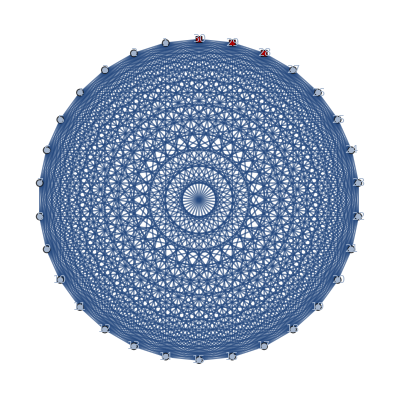

```mathematica
graph=CompleteGraph[numberOfEvents+numberOfGates,
VertexShapeFunction->verticesGatesShape,
VertexSize->0.2,
VertexStyle->verticesGatesColor,
VertexLabels->Placed["Name",Center]]
```

```mathematica
edgeList=DeleteDuplicates[SortBy[List@@@EdgeList[graph],First]];
```

```mathematica
vertexList=VertexList[graph];
```

```mathematica
alpha1=10;
alpha2=20;
alpha3=30;
```

### Определения предка события

```mathematica
successorsPairs=Flatten[Partition[#,2,1]&/@events,1]
```

{{1,2},{2,3},{4,5},{5,6},{7,8},{8,9},{10,11},{12,13},{13,14},{15,16},{16,17},{18,19},{20,21},{21,22},{23,24},{24,25},{26,27}}

```mathematica
Clear[u,event,successor]

Do[
{successor,event}=pair;
u[event]=successor,
{pair,successorsPairs}
]
```

### Определение веса

```mathematica
Clear[getWeightMatrix]
getWeightMatrix[{vertexList_:vertexList,edgeList_:edgeList},
			u_:u,
			{tmin_:tmin,numberOfEvents_:numberOfEvents,distanceMatrix_:distanceMatrix,preferences_:preferences},
			{alpha1_:alpha1,alpha2_:alpha2,alpha3_:alpha3}]:=Module[
{
weightMatrix=SparseArray[{{i_,j_}:>0},{Length[vertexList],Length[vertexList]}],
i,j
},
Do[
{i,j}=edge;
If[
i<=numberOfEvents∧j<=numberOfEvents,
If[
distanceMatrix⟦i,j⟧<0,
weightMatrix⟦i,j⟧=-∞,
If[
distanceMatrix⟦i,j⟧>=0∧(u[i]===j∨u[j]===i),
weightMatrix⟦i,j⟧=alpha2,
If[
distanceMatrix⟦i,j⟧>=0∧u[i]=!=u[j]∧u[j]=!=u[i],
weightMatrix⟦i,j⟧=alpha3*Max[tmin-distanceMatrix⟦i,j⟧,0]
]
]
],
If[
i<=numberOfEvents∧j>numberOfEvents,
If[
preferences⟦i,j-numberOfEvents⟧==-∞,
weightMatrix⟦i,j⟧=-∞,
weightMatrix⟦i,j⟧=alpha1*preferences⟦i,j-numberOfEvents⟧
],
weightMatrix⟦i,j⟧=-∞
]
],
{edge,edgeList}
];
weightMatrix
]
```

```mathematica
weightMatrix=getWeightMatrix[{vertexList,edgeList},u,{tmin,numberOfEvents,distanceMatrix,preferences},{alpha1,alpha2,alpha3}];
```

```mathematica
fullWeightMatrix=#+#ᵀ&@UpperTriangularize[weightMatrix];
```

### Целевая функция

```mathematica
Clear[targetFunction]
targetFunction[solution_,weightMatrix_]:=Module[
{
cliqueEdges=Partition[#,2,1,1]&/@solution
},
Total[Apply[fullWeightMatrix⟦##⟧&,cliqueEdges,{2}],2]
]
```

### Детерминированное начальное разбиение

```mathematica
Clear[h]
h[i_,C_,D_]:=Subtract@@Composition[Total,Map[fullWeightMatrix⟦i,#⟧&,#]&]/@{D,Complement[C,{i}]}
```

```mathematica
Clear[getAssignmentData]
getAssignmentData[clique_,nontabu_,u_,h_]:=Module[
{
currentSum,currentC,prevC,prevPrevC,
maxSum=-∞,maxVertex=0,maxD={}
},
Do[
currentC=clique⟦FirstPosition[clique,i]⟦1⟧⟧;
prevC=clique⟦FirstPosition[clique,u[i]]⟦1⟧⟧;
prevPrevC=clique⟦FirstPosition[clique,u[u[i]]]⟦1⟧⟧;
currentSum=h[i,currentC,D]+h[u[i],prevC,D]+h[u[u[i]],prevPrevC,D];
If[
currentSum>maxSum,
maxSum=currentSum;
maxVertex=i;
maxD=D;
],
{i,nontabu},
{D,clique}
];
{maxSum,maxVertex,maxD}
]
```

```mathematica
Clear[initialSolution]
initialSolution[vertexList_,u_,h_]:=Module[
{
clique=Partition[vertexList,1,1],
mask=Thread[And[Composition[NumberQ,u,u]/@vertexList,Composition[NumberQ,u]/@vertexList]],
tabu,nontabu,
maxSum,maxVertex,maxD,maxVertices,value
},
nontabu=Pick[vertexList,mask];
tabu=Complement[vertexList,nontabu];
While[
nontabu=!={},
{maxSum,maxVertex,maxD}=getAssignmentData[clique,nontabu,u,h];
If[
maxSum>0,
{maxSum,maxVertex,maxD}=getAssignmentData[clique,nontabu,u,h];
maxVertices={maxVertex,u[maxVertex],u[u[maxVertex]]};
value=DeleteDuplicates[clique⟦FirstPosition[clique,maxD]⟦1⟧⟧~Join~maxVertices];
clique⟦FirstPosition[clique,maxD]⟦1⟧⟧=value;
clique=DeleteCases[#,x_/;AnyTrue[value,x==#&]]&/@Complement[clique,value];
AppendTo[clique,value];
];
nontabu=DeleteCases[nontabu,maxVertex];
AppendTo[tabu,maxVertex];
];
DeleteCases[Sort/@clique,{}]
]
```

```mathematica
feasibleSolution=initialSolution[vertexList,u,h]
targetFunction[feasibleSolution,fullWeightMatrix]
```

{{10},{11},{13},{14},{18},{19},{26},{27},{12,15,16,17},{7,8,9,29},{23,24,25,30},{1,2,3,4,5,6,28},{20,21,22}}

1340

### Случайное начальное разбиение

```mathematica
Clear[randomInitialSolution]
randomInitialSolution[vertexList_,maxNumberInPart_:10,weightMatrix_]:=Module[
{
vertexCount=Length[vertexList],
shuffle=RandomSample[vertexList],
random,
cliques={},
i=1
},
While[i<vertexCount,
random=RandomInteger[Quotient[vertexCount,maxNumberInPart]];
If[i+random<vertexCount,
AppendTo[cliques,shuffle⟦i;;i+random⟧];
i+=random+1,
AppendTo[cliques,shuffle⟦i;;vertexCount⟧];
i=vertexCount]
];
If[Length[Flatten[cliques]]!=vertexCount∨targetFunction[cliques,weightMatrix]==-∞,
randomInitialSolution[vertexList,maxNumberInPart,weightMatrix],
cliques]
]
```

```mathematica
randomSolution=randomInitialSolution[vertexList,fullWeightMatrix]
```

{{11,26,18},{17,7},{6},{19,23},{4,1},{3,24,12},{22},{29,9,27},{13,25},{21},{5},{15,14},{10,16,28,2},{30},{8,20}}

### Сравнение начальных разбиений (самоутверждение)

```mathematica
feasibleTFValue=targetFunction[feasibleSolution,fullWeightMatrix];
randomTFValue=targetFunction[randomSolution,fullWeightMatrix];

Style[
Grid[
{{"Название","Значение ЦФ"},
{"Детерминированное НР",feasibleTFValue},
{"Случайное НР",randomTFValue},
Style[#,Red]&/@{"∆",feasibleTFValue-randomTFValue}},
Frame->All,
Background->{None,{LightPurple}}],
FontSize->16,FontFamily->"Times New Roman"]
```

Название | Значение ЦФ
Детерминированное НР | 1340
Случайное НР | 760
∆ | 580

### Алгоритм локального поиска

```mathematica
Clear[localSearch]
localSearch[solution_,numberOfIterations_,vertexList_,weightMatrix_]:=Module[
{
currentSolution=solution,
candidateSolution,
cliqueVariants,withoutVertex,selectedVertex,
cliquesTargetFunctionValue,
maxElementPosition,maxTargetFunctionValue
},
Do[
selectedVertex=RandomChoice[vertexList];
cliqueVariants=Table[
withoutVertex=Append[DeleteCases[currentSolution,selectedVertex,{2}],{}];
AppendTo[withoutVertex⟦i⟧,selectedVertex];
withoutVertex,
{i,Length[currentSolution]+1}];
cliquesTargetFunctionValue=targetFunction[#,weightMatrix]&/@cliqueVariants;
maxTargetFunctionValue=Max[cliquesTargetFunctionValue];
If[maxTargetFunctionValue!=-∞,
maxElementPosition=FirstPosition[cliquesTargetFunctionValue,Max[maxTargetFunctionValue]]⟦1⟧;
candidateSolution=DeleteCases[cliqueVariants⟦maxElementPosition⟧,{}];
If[maxTargetFunctionValue>targetFunction[currentSolution,weightMatrix],
currentSolution=candidateSolution],
Continue[]],
numberOfIterations];
currentSolution
]
```

```mathematica
localSearchSolution=localSearch[feasibleSolution,1000,vertexList,fullWeightMatrix]
targetFunction[localSearchSolution,fullWeightMatrix]
```

{{10,2},{13,6},{18,19},{27,11},{12,15,16,17,5},{7,8,9,29},{23,24,25,30,26},{1,3,4,28},{20,21,22,14}}

2000

### Алгоритм имитации отжига

Функции изменения температуры

```mathematica
Clear[logarithmicSchedule]
Options[logarithmicSchedule]={CoolingSpeed->1.(*>=1*)};
logarithmicSchedule[temp_?NumberQ,iteration_,OptionsPattern[]]:=temp/(OptionValue[CoolingSpeed] Log[iteration+1]+1)
```

```mathematica
Clear[geometricSchedule]
Options[geometricSchedule]={CoolingSpeed->0.85(*[0.8,0.9]*)};
geometricSchedule[temp_?NumberQ,iteration_,OptionsPattern[]]:=OptionValue[CoolingSpeed]^iteration temp
```

```mathematica
Clear[linearSchedule]
Options[linearSchedule]={CoolingSpeed->0.85(*>0*)};
linearSchedule[temp_?NumberQ,iteration_,OptionsPattern[]]:=temp/(1+OptionValue[CoolingSpeed] iteration)
```

```mathematica
Clear[quadraticSchedule]
Options[quadraticSchedule]={CoolingSpeed->0.85(*>0*)};
quadraticSchedule[temp_?NumberQ,iteration_,OptionsPattern[]]:=temp/(1+OptionValue[CoolingSpeed] iteration^2)
```

```mathematica
Clear[getCandidate]
getCandidate[currentSolution_,selectedVertex_,weightMatrix_]:=Module[
{
cliqueVariants,
withoutVertex,
candidateSolution
},
While[True,
cliqueVariants=Table[
withoutVertex=Append[DeleteCases[currentSolution,selectedVertex,{2}],{}];
AppendTo[withoutVertex⟦i⟧,selectedVertex];
withoutVertex,
{i,Length[currentSolution]+1}];
If[AllTrue[targetFunction[#,weightMatrix]&/@cliqueVariants,#==-∞&],
Print["Stop by wrong vertex"];
Break[]];
candidateSolution=DeleteCases[RandomChoice[cliqueVariants],{}];
If[targetFunction[candidateSolution,weightMatrix]!=-∞,Break[]];
];
candidateSolution
]
```

```mathematica
Clear[simulatedAnnealing]
simulatedAnnealing[solution_,{tMin_,tMax_,temperatureFunction_},vertexList_,weightMatrix_]:=Module[
{
tCurrent=tMax,
currentSolution=solution,
selectedVertex,withoutVertex,cliqueVariants,candidateSolution,
differenceTargetFunctions,i=1
},
While[tCurrent>tMin,
selectedVertex=RandomChoice[vertexList];
candidateSolution=getCandidate[currentSolution,selectedVertex,weightMatrix];
differenceTargetFunctions=targetFunction[candidateSolution,weightMatrix]-targetFunction[currentSolution,weightMatrix];
If[differenceTargetFunctions>0,
currentSolution=candidateSolution,
If[RandomReal[]<Exp[differenceTargetFunctions/tCurrent],
currentSolution=candidateSolution]
];
tCurrent=temperatureFunction[tCurrent,i];
i+=1;
];
currentSolution
]
```

```mathematica
feasibleSolution
targetFunction[feasibleSolution,fullWeightMatrix]
```

{{10},{11},{13},{14},{18},{19},{26},{27},{12,15,16,17},{7,8,9,29},{23,24,25,30},{1,2,3,4,5,6,28},{20,21,22}}

1340

```mathematica
simulatedAnnealingSolution=simulatedAnnealing[feasibleSolution,{0.5,10,logarithmicSchedule},vertexList,fullWeightMatrix]
targetFunction[simulatedAnnealingSolution,fullWeightMatrix]
```

{{10,13},{11},{14},{18},{19},{26},{27},{12,15,16,17,24},{7,8,9,29},{23,25,30},{1,2,3,4,5,6,28},{20,21,22}}

1360

### Алгоритм поиска с запретом

```mathematica
Clear[getCandidateList]
getCandidateList[currentSolution_,vertexList_]:=Module[
{
withoutVertex
},
Table[
Table[
withoutVertex=Append[DeleteCases[currentSolution,v,{2}],{}];
AppendTo[withoutVertex⟦i⟧,v];
DeleteCases[withoutVertex,{}],
{i,Length[currentSolution]+1}],
{v,vertexList}]
]
```

```mathematica
Clear[getDifferenceMatrix]
getDifferenceMatrix[currentSolution_,candidateList_,weightMatrix_]:=Map[targetFunction[#,weightMatrix]-targetFunction[currentSolution,weightMatrix]&,candidateList,{2}]
```

```mathematica
Clear[tabuSearch]
tabuSearch[solution_,numberOfIterations_,weightMatrix_,vertexList_]:=Module[
{
currentSolution=solution,
candidateList,candidateSolution,
M,
vertex,clique,
tabu={}
},
Do[
candidateList=getCandidateList[currentSolution,vertexList];
M=getDifferenceMatrix[currentSolution,candidateList,weightMatrix];
If[Max[M]<0,
Print["Stop by negative difference"];
Break[],
{vertex,clique}=FirstPosition[M,Max[M]]
];
candidateSolution=candidateList⟦vertex,clique⟧;
While[candidateList!={}∧MemberQ[candidateSolution,tabu],
Print["Go in"];
candidateList=DeleteCases[candidateList,candidateSolution,{2}];
M=getDifferenceMatrix[currentSolution,candidateList,weightMatrix];
If[Max[M]<=0,
Print["Stop by nonpositive difference"];
Break[],
{vertex,clique}=FirstPosition[M,Max[M]]
];
candidateSolution=candidateList⟦vertex,clique⟧;
If[candidateList=={}∨!MemberQ[candidateSolution,tabu],Break[]]
];
currentSolution=candidateSolution;
AppendTo[tabu,candidateSolution],
numberOfIterations];
currentSolution
]
```

```mathematica
tabuSearchSolution=tabuSearch[feasibleSolution,30,fullWeightMatrix,vertexList]
```

{{10,2},{13,6},{14,20},{26},{27,11},{12,15,16,17,5},{7,8,9,29},{23,24,25,30,19,18},{3,4,28,1},{21,22}}

```mathematica
targetFunction[tabuSearchSolution,fullWeightMatrix]
targetFunction[feasibleSolution,fullWeightMatrix]
```

2080

1340

### Сравнение алгоритмов

```mathematica
Style[
Grid[
{{"Название","Значение ЦФ"},
{"Начальное решение",targetFunction[feasibleSolution,fullWeightMatrix]},
{"Локальный поиск",targetFunction[localSearchSolution,fullWeightMatrix]},
{"Имитация отжига",targetFunction[simulatedAnnealingSolution,fullWeightMatrix]},
{"Поиск с запретами",targetFunction[tabuSearchSolution,fullWeightMatrix]}},
Frame->All,
Background->{None,{LightPurple}}],
FontSize->16,FontFamily->"Times New Roman"]
```

Название | Значение ЦФ
Начальное решение | 1340
Локальный поиск | 2000
Имитация отжига | 1360
Поиск с запретами | 2080

```mathematica
solutions={localSearchSolution,simulatedAnnealingSolution,tabuSearchSolution};
colors=RandomColor[Length[#]]&/@solutions;
edgesSolutions=Map[Partition[#,2,1,1]&,solutions,{2}];
edgesSolutionsColors=MapIndexed[UndirectedEdge@@#1->{colors⟦Sequence@@(#2⟦1;;2⟧)⟧,Thickness[0.01],Opacity[1]}&,edgesSolutions,{3}];

Panel[Manipulate[
Show[CompleteGraph[numberOfEvents+numberOfGates,
VertexShapeFunction->verticesGatesShape,
VertexSize->0.5,
VertexStyle->verticesGatesColor,
EdgeStyle->{Opacity[showEdges],Sequence@@Flatten[edgesSolutionsColors⟦algorithm⟧]},
VertexLabels->Placed["Name",Center]],ImageSize->Large],
Row[{Control[{{algorithm,1,"Алгоритм: "},{1->"Локальный поиск",2->"Имитация отжига",3->"Поиск с запретами"},RadioButton}]}],
Row[{Control[{{showEdges,1,"Рёбра: "},{0,1}}]}],
Paneled->False],
Style["Визуализация решений",20,Bold,FontFamily->"Times New Roman"]]
```

Визуализация решений